<|
"Title"→"Symbolic Algebra",
"Slug"→Automatic,
"Path"→"Using Mathematica/Useful Features",
"ID"→"1.3.2",
"Date"→"Thu 28 Dec 2017 02:19:10""GMT"-7.,
"Modified"→Now,
"Authors"→{},
"Categories"→{"using-mathematica","useful-features"},
"Tags"→{"symbolic algebra"},
"ExportOptions"→{"Save"→True}
|>

### Symbolic Algebra

As is explained more fully in the Mathematica Programming section, the language Mathematica is built around is almost 100% symbolic, which makes it perfect for algebraic manipulations.

One of the simplest examples of things one can do in Mathematica is generate and combine polynomials:

```mathematica
simplePolynomial[var_,order_]:=
	Total@Table[RandomInteger[10]*Power[var,n],{n,order}];
```

We’ll make a few of these polynomials and add them:

```mathematica
pX1=simplePolynomial[x,2]
pX2=simplePolynomial[x,2]
pX1+pX2
```

6 x+6 x^2

8 x+9 x^2

14 x+15 x^2

This works just as well at any polynomial order. Here we’ll add five randomly generated polynomials of order less than or equal to 15.

```mathematica
Array[(simplePolynomial[x, RandomInteger[15]])&, 5]//Total
```

22 x+26 x^2+15 x^3+28 x^4+10 x^5+9 x^6+12 x^7+13 x^8+19 x^9+11 x^10+9 x^11+13 x^12+6 x^13+4 x^14

Here’s that again, but formatted nicer:

22 x+26 x^2+15 x^3+28 x^4+10 x^5+9 x^6+12 x^7+13 x^8+19 x^9+11 x^10+9 x^11+13 x^12+6 x^13+4 x^14

For those interested, the & specifies that what comes before should be treated as a function, but absent any variables we simply get our expression as a result.

#### Simplify

For more complex things we’ll need to explicitly simplify them:

```mathematica
sphericalHarmonicSum=
	Total@
		Array[
		SphericalHarmonicY[RandomInteger[5], RandomInteger[5], θ, ϕ]&,
		5]
```

We can then have Mathematica simplify this expression for us more:

```mathematica
Simplify[sphericalHarmonicSum]
```

1/64 ⅇ^(ⅈ ϕ) √(3/(2 π)) Sin[θ] (-32+2 √35 (4+√11) ⅇ^(ⅈ ϕ) Sin[2 θ]+3 √385 ⅇ^(ⅈ ϕ) Sin[4 θ])

Sometimes we also need to use the function FullSimplify to get everything simplified:

```mathematica
FullSimplify[sphericalHarmonicSum]
```

1/32 ⅇ^(ⅈ ϕ) √(3/(2 π)) Sin[θ] (-16+√35 ⅇ^(ⅈ ϕ) (4+√11+3 √11 Cos[2 θ]) Sin[2 θ])

It often makes sense to go for Simplify over FullSimplify, despite the fact that we can get more simplification out of FullSimplify, because sometimes the Simplify is all we need to see a pattern ourselves, while FullSimplify can over-simplify and obliterate that pattern.

It’s good to keep in mind that while Mathematica may know more than we do, we're still smarter than it is.

#### Solve

Mathematica can also solve equations for us. We’ll try this on a nice quartic polynomial:

```mathematica
polynomialInX=simplePolynomial[x, 4]
```

6 x+5 x^2+3 x^3+6 x^4

Note that there’s no nice way to find the roots of this polynomial by hand. But Mathematica doesn’t mind:

```mathematica
Solve[polynomialInX==0,x]
```

{
	{x→0},
	{x→1/6 (-1-9/(-94+√9565)^(1/3)+(-94+√9565)^(1/3))},
	{x→-1/6+(3 (1+ⅈ √3))/(4 (-94+√9565)^(1/3))-1/12 (1-ⅈ √3) (-94+√9565)^(1/3)},
	{x→-1/6+(3 (1-ⅈ √3))/(4 (-94+√9565)^(1/3))-1/12 (1+ⅈ √3) (-94+√9565)^(1/3)}
	}

Here’s one of those solutions in easier-to-read form:

1/6 (-1-9/(-94+√9565)^(1/3)+(-94+√9565)^(1/3))

As mentioned before, Mathematica knows more math than any of us. It sees a quartic polynomial and knows that by the fundamental theorem of algebra there are four solutions to this equation, we just might need to find complex solutions.

Usually this isn’t what we want, unfortunately. Happily Mathematica can dumb itself down for us.

```mathematica
Solve[polynomialInX==0,x,Reals]
```

{ {x→0},{x→Root[6+5 #1+3 #1^2+6 #1^3&,1]} }

Notice that we get this odd Root expression. That’s the way Mathematica represents a perfectly exact root. We can get its numerical one of two ways. Either we make the equation inexact:

```mathematica
Solve[polynomialInX==0., x, Reals]
```

{ {x→-0.867733},{x→0} }

Or we numericize after the fact:

```mathematica
N[Solve[polynomialInX==0,x,Reals],6]
```

{ {x→0},{x→-0.867733} }

One useful thing to know with Solve is why the results are returned so oddly. Each list is a different solution, which is more important with multivariate equations, which we’ll get to, but first let’s see a nice way to get out our solutions in a simple list:

```mathematica
x/.N[Solve[polynomialInX==0,x,Reals],6]
```

{0,-0.867733}

The /. is an alias for ReplaceAll, which is described in more detail later in the Replacement Patterns section. For now let’s just note that any time it sees var on the left hand side it looks for var→val on the right hand side and replaces var with that.

Now let’s also see how we can plot these solutions:

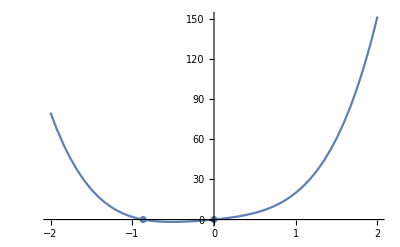

```mathematica
Show[
	Plot[polynomialInX,{x,-2,2}],
	ListPlot[Table[{x,0},
		{x,x/.Solve[polynomialInX==0.,x,Reals]}]]
	]
```

We have to use ListPlot to plot our discrete solutions, but we can see we get the result we expect.

We could even write a function that will solve the equation for an arbitrary value and plot the result:

```mathematica
solveAndPlot[eqInX_,val_]:=
	Show[
		Plot[eqInX,{x,-2,2}],
		ListPlot[Table[{x,val},
			{x,x/.Solve[eqInX==(1.val),x,Reals]}]],
		PlotLabel->
			Row@{
				HoldForm[eqInX==val]," @ ",
				Row@Riffle[(x/.Solve[eqInX==(1.val),x,Reals]),", "]
				}
		];
```

Calling this on our solution:

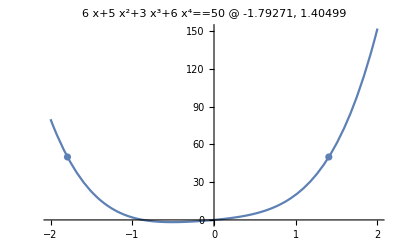

```mathematica
solveAndPlot[polynomialInX,50]
```

But that’s getting distracted, I suppose.

#### Multivariate Solve

Let’s move to multivariate equations now:

```mathematica
polynomialInXandY=simplePolynomial[x,3]+simplePolynomial[y,3]
```

8 x+2 x^2+2 y+10 y^2+8 y^3

8 x+2 x^2+2 y+10 y^2+8 y^3

It can still solve this equation, although as it will admit, it may miss some solutions.

```mathematica
Solve[polynomialInXandY == 0,{x,y}, Reals]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{ {x→ConditionalExpression[-2-√(4-y-5 y^2-4 y^3),y<1/12 (-5+(829-6 √19029)^(1/3)+(829+6 √19029)^(1/3))]},{x→ConditionalExpression[-2+√(4-y-5 y^2-4 y^3),y<1/12 (-5+(829-6 √19029)^(1/3)+(829+6 √19029)^(1/3))]},{x→-2-√(4+1/12 (5-(829-6 √19029)^(1/3)-(829+6 √19029)^(1/3))-5/144 (-5+(829-6 √19029)^(1/3)+(829+6 √19029)^(1/3))^2-1/432 (-5+(829-6 √19029)^(1/3)+(829+6 √19029)^(1/3))^3),y→1/12 (-5+(829-6 √19029)^(1/3)+(829+6 √19029)^(1/3))} }

Here’s one of the branches in human-readable form:

-2-√(4+1/12 (5-(829-6 √19029)^(1/3)-(829+6 √19029)^(1/3))-5/144 (-5+(829-6 √19029)^(1/3)+(829+6 √19029)^(1/3))^2-1/432 (-5+(829-6 √19029)^(1/3)+(829+6 √19029)^(1/3))^3)

Note that it also gives us these odd ConditionalExpression statements. This is because the solution could branch depending on how x and y interplay. Let’s just get take one of these solutions:

```mathematica
conditionalSoln=First[x/.Solve[polynomialInXandY == 0.,{x,y}, Reals]];
N[conditionalSoln]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

ConditionalExpression[-2.-1. √(4.-1. y-5. y^2-4. y^3),y<0.660936]

And plot it:

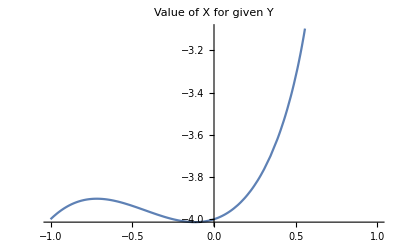

```mathematica
Plot[conditionalSoln,{y,-1,1},PlotLabel->"Value of X for given Y"]
```

We can force a given branch of this conditional expression, however, by telling Mathematica what it can assume.

#### Assumptions

When Mathematica simplifies an expression it checks what we’ve told it to about the expression. It does that by looking at the value of the variable $Assumptions

```mathematica
$Assumptions
```

True

This is the default value. But we can make it assume things for us. Let’s assume that y satifies our ConditionalExpression. First we set the Assumptions:

```mathematica
$Assumptions=y<.5
```

y<0.5

Now Mathematica will use these when solving:

```mathematica
xAndyRoots={x, y}/.Solve[polynomialInXandY == 0, {x, y}, Reals]//First//Simplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{-2-√(4-y-5 y^2-4 y^3),y}

And when we’re done we simply reset the $Assumptions variable. We can also apply $Assumptions to a single Simplify expression or similar, but I will leave that to you to read up on.

### See Also:

Symbolic Calculations

Simplifying Algebraic Expressions

Simplifying With Assumptions

Putting Expressions into Different Forms

Using Assumptions

Mathematica as Mathematician’s Aid

Integration